## Coulomb Potential

```mathematica
ClearAll["Global`*"]
```

Constants/Parameters

```mathematica
(*Constants (In Atomic Units)*)
m:=1
ℏ:=1
ke:=1    (*1/(4 π ϵ0)*)
e:=1


(*Parameters*)
l:=1
L:=50
T:=1000
fps:=60
numstates:=4
```

Definitions

```mathematica
(*Potential Energy*)
V[x_]:=-(ke e^2)/x+ℏ^2/(2 m) (l (l+l))/x^2 ;

(*Time Independent Schrodinger Equation*)
H=-ℏ^2/(2 m) ψ''[x]+V[x]*ψ[x];
```

Energy Eigenvalues/Eigenfunctions

{{-0.0210927,-0.0312869},{InterpolatingFunction[…][x],InterpolatingFunction[…][x]}}

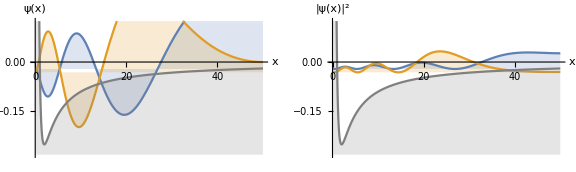

```mathematica
(*{vals,funs}=NDEigensystem[H,ψ[x],{x,0,L},numstates,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}}];*)
{vals,funs}=NDEigensystem[H,ψ[x],{x,0,L},numstates,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}},"Eigensystem"->{"FEAST","Interval"->{V[(2 l^2 ℏ^2)/(e^2 ke m)],V[L]}}}]

(*Since the potential tends to 0 too slowly, only use eigenvalues that are less than the value of the potential at the right boundary of the region to ensure we're getting bound states*)
boundindices:=Flatten[Position[vals,_?(#<V[L]&)]]
boundvals:=vals[[boundindices]]
boundfuns:=funs[[boundindices]]
numboundstates:=Length[boundvals]

lower:=V[(2 l^2 ℏ^2)/(e^2 ke m)]+Min[boundvals]
upper:=Max[Map[FindMaxValue[{#,0<=x≤L},x]&,boundfuns]]
bounds:={lower,upper}

fillingrule:=Table[i->boundvals[[i]],{i,1,numboundstates}]
labels:=Table[ToString[Subscript[ψ, i],TraditionalForm],{i,1,numboundstates}]
title:=StringForm["Coulomb Potential: First `` Bound Stationary States",numboundstates]

GraphicsRow[{Show[Plot[Evaluate[boundfuns+boundvals],{x,0,L},AxesLabel->{"x","ψ(x)"},Filling->fillingrule,PlotRange->bounds],Plot[V[x],{x,0,L},Filling->Bottom,PlotRange->bounds,PlotStyle->Gray]],Show[Plot[Evaluate[boundfuns^2+boundvals],{x,0,L},AxesLabel->{"x","|ψ(x)|^2"},Filling->fillingrule,PlotRange->bounds],Plot[V[x],{x,0,L},Filling->Bottom,PlotRange->bounds,PlotStyle->Gray]]},PlotLabel->title,ImageSize->Large]
```

Stationary States

```mathematica
ϵn[n_]:=Part[boundvals,n];
ψn[n_]:=Part[boundfuns,n];
Ψn[n_]:=ψn[n] Exp[-ℏ ϵn[n] t/I];
```

Mixed State

```mathematica
ψ=ψn[1]+ψn[3]+ψn[4];
Ψ=Ψn[1]+Ψn[3]+Ψn[4];

norm=Sqrt[NIntegrate[(Conjugate[ψ] ψ),{x,0,L}]];
Ψ=Ψ/norm;
```

Part::partw: Part 3 of {InterpolatingFunction[{{0.,50.}},{5,4225,0,{10001},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[«1»]},{1.22124×10^-9,-5.50723×10^-6,-0.0000219194,-0.0000490722,-0.0000868031,-0.000134951,«40»,-0.00926254,-0.00961939,-0.0099809,-0.010347,«9951»},{Automatic}][x],«1»} does not exist.

Part::partw: Part 4 of {InterpolatingFunction[{{0.,50.}},{5,4225,0,{10001},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[«1»]},{1.22124×10^-9,-5.50723×10^-6,-0.0000219194,-0.0000490722,-0.0000868031,-0.000134951,«40»,-0.00926254,-0.00961939,-0.0099809,-0.010347,«9951»},{Automatic}][x],«1»} does not exist.

Part::partw: Part 3 of {InterpolatingFunction[{{0.,50.}},{5,4225,0,{10001},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[«1»]},{1.22124×10^-9,-5.50723×10^-6,-0.0000219194,-0.0000490722,-0.0000868031,-0.000134951,«40»,-0.00926254,-0.00961939,-0.0099809,-0.010347,«9951»},{Automatic}][x],«1»} does not exist.

Part::partw: Part 3 of {-0.0210927,-0.0312869} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 3 of {InterpolatingFunction[{{0.,50.}},{5,4225,0,{10001},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[«1»]},{1.22124×10^-9,-5.50723×10^-6,-0.0000219194,-0.0000490722,-0.0000868031,-0.000134951,«40»,-0.00926254,-0.00961939,-0.0099809,-0.010347,«9951»},{Automatic}][x],«1»} does not exist.

Part::partw: Part 4 of {InterpolatingFunction[{{0.,50.}},{5,4225,0,{10001},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[«1»]},{1.22124×10^-9,-5.50723×10^-6,-0.0000219194,-0.0000490722,-0.0000868031,-0.000134951,«40»,-0.00926254,-0.00961939,-0.0099809,-0.010347,«9951»},{Automatic}][x],«1»} does not exist.

NIntegrate::inumr: The integrand Conjugate[{«1»}⟦3⟧+«1»+InterpolatingFunction[{{0.,50.}},{5,4225,0,{10001},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[{«1»},«3»]},{1.22124×10^-9,-5.50723×10^-6,-0.0000219194,-0.0000490722,-0.0000868031,«41»,-0.00926254,-0.00961939,-0.0099809,-0.010347,«9951»},{Automatic}][x]] «1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,50}}.

Part::partw: Part 3 of {InterpolatingFunction[{{0.,50.}},{5,4225,0,{10001},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[«1»]},{1.22124×10^-9,-5.50723×10^-6,-0.0000219194,-0.0000490722,-0.0000868031,-0.000134951,«40»,-0.00926254,-0.00961939,-0.0099809,-0.010347,«9951»},{Automatic}][x],«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NIntegrate::inumr: The integrand Conjugate[{«1»}⟦3⟧+«1»+InterpolatingFunction[{{0.,50.}},{5,4225,0,{10001},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[{«1»},«3»]},{1.22124×10^-9,-5.50723×10^-6,-0.0000219194,-0.0000490722,-0.0000868031,«41»,-0.00926254,-0.00961939,-0.0099809,-0.010347,«9951»},{Automatic}][x]] «1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,50}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::partw: Part 3 of {InterpolatingFunction[{{0.,50.}},{5,4225,0,{10001},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[«1»]},{1.22124×10^-9,-5.50723×10^-6,-0.0000219194,-0.0000490722,-0.0000868031,-0.000134951,«40»,-0.00926254,-0.00961939,-0.0099809,-0.010347,«9951»},{Automatic}][x],«1»} does not exist.

Part::partw: Part 4 of {InterpolatingFunction[{{0.,50.}},{5,4225,0,{10001},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[«1»]},{1.22124×10^-9,-5.50723×10^-6,-0.0000219194,-0.0000490722,-0.0000868031,-0.000134951,«40»,-0.00926254,-0.00961939,-0.0099809,-0.010347,«9951»},{Automatic}][x],«1»} does not exist.

Part::partw: Part 3 of {InterpolatingFunction[{{0.,50.}},{5,4225,0,{10001},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[«1»]},{1.22124×10^-9,-5.50723×10^-6,-0.0000219194,-0.0000490722,-0.0000868031,-0.000134951,«40»,-0.00926254,-0.00961939,-0.0099809,-0.010347,«9951»},{Automatic}][x],«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NIntegrate::inumr: The integrand Conjugate[{«1»}⟦3⟧+«1»+InterpolatingFunction[{{0.,50.}},{5,4225,0,{10001},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[{«1»},«3»]},{1.22124×10^-9,-5.50723×10^-6,-0.0000219194,-0.0000490722,-0.0000868031,«41»,-0.00926254,-0.00961939,-0.0099809,-0.010347,«9951»},{Automatic}][x]] «1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,50}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
animation:=Animate[Show[Plot[Evaluate[Conjugate[Ψ] Ψ]+(ϵn[1]+ϵn[3]+ϵn[4])/.t->s,{x,0,L},Axes->True,AxesLabel->{"x","|ψ(x)|^2"},PlotRange->bounds,PlotStyle->Red],Plot[V[x],{x,0,L},Filling->Axis,PlotStyle->Black,Exclusions->None]],{s,0,T},DisplayAllSteps->True,DefaultDuration->T,AnimationRunning->False];
animation
```